```mathematica
SetDirectory["~/Cellular-Automata"];
Width=16;
Height=32;
makePic[Width_,Height_,data_]:=Table[{If[data[[j,i]]==1,Black,White],Polygon[{{i,-j},{i+1,-j},{(data[[j+1,Width+1]]-1)(i+1)-(data[[j+1,Width+1]]-2)9,-j-1},{(data[[j+1,Width+1]]-1)(i)-(data[[j+1,Width+1]]-2)9,-j-1}}]},{i,1,Width},{j,1,Height}];
Run["./RunSim -s 137 -b -e 4"];
data=Import["./rule_num_30.csv"];
```

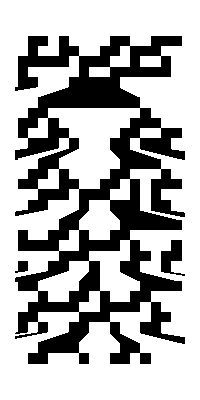

```mathematica
pic=makePic[Width,Height,data];
(*Export["rule_num_30.gif",Graphics[pic,PlotRange->{{1,17},All}]]*)
Graphics[pic,PlotRange->{{1,Width+1},All}]
```

```mathematica
Do[
data=Import["./rule_num_"<>ToString[k]<>".csv"];
Export["rule_num_"<>ToString[k]<>".gif",
Graphics[makePic[Width,Height,data],
PlotRange->{{1,Width+1},All}]],{k,0,255,1}]
```